# Billiards

```mathematica
Get[NotebookDirectory[]<>"../Kernel/init.m"] (*Load QuantumWalks package*)

Print["Last update: "<>DateString[{"Day"," ","MonthName"," ","Year"}]]
```

Last update: 25 February 2026

## Routines’ details and usage examples

## BuildShiftOperators[gridData,opts]

constructs the shift operators of a DTQW for a given grid geometry. These operators move the quantum walker between adjacent nodes while implementing unitary bounce-back boundary conditions—if the walker hits the edge of the billiard, it reflects into the opposite internal state to preserve the total probability.

For a grid provided via gridData, it returns the operators based on the chosen CoinDimension:

CoinDimension -> 2 (Default): Returns a list of two matrices {Sx, Sy} for a split-step quantum walk.

Sx: Horizontal conditional shift.

Sy: Vertical conditional shift.

CoinDimension -> 4: Returns a single global matrix S for a 4-coin-state DTQW.

Internal states are encoded as: 1:Up (+y), 2:Down (−y), 3:Right (+x), 4:Left (−x).

Note 1: All operators are returned as SparseArray objects to ensure high performance in large-scale simulations.

Note 2: gridData may be any other geometry with the same structure as that the output of functions Generate...Basis.

### Usage example

Constructing operators for a split-step walk on a Bunimovich stadium (L=10,R=15):

```mathematica
(*1. Generate the grid*)
BunimovichData=GenerateBunimovichBasis[10,15];

(*2. Build 2-state split-step operators (default)*)
{Sx,Sy}=BuildShiftOperators[BunimovichData];
```

The horizontal shift operator Sx structure:

```mathematica
(* Check the dimensions (2 states per spatial node) *)
Dimensions[Sx]

(* Verify that the operator is Unitary *)
UnitaryMatrixQ[Sx]
```

{706,706}

True

Constructing a single global operator for a 4-state walk:

```mathematica
(* Build 4-state Grover shift operator *)
SGlobal = BuildShiftOperators[BunimovichData, CoinDimension -> 4];

(* Check the dimensions (4 states per spatial node) *)
Dimensions[SGlobal]
```

{1412,1412}

Obtain the total number of non-zero entries to verify sparsity:

```mathematica
ArrayRules[SGlobal] // Length
```

1413

## GeneralizedGroverCoin[θ]

yields the 4×4 anisotropic Grover coin matrix 2*∣s(θ)⟩⟨s(θ)∣ - I_4, with ∣s(θ)⟩= 1/√2{cos(θ),cos(θ),sin(θ),sin(θ)}.

### Usage example

Generating a standard Grover coin (θ=π/4):

```mathematica
MatrixForm[GroverCoin=GeneralizedGroverCoin[Pi/4]]
```

(-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2)

Verify GroverCoin is unitary:

```mathematica
(* Verify unitarity *)
UnitaryMatrixQ[GroverCoin]
(* Output: True *)
```

True

## BlockDiagonalCoin[ϕ]

yields a 4×4 block-diagonal rotation coin matrix:

### Usage example

Generating the block-diagonal coin with a ϕ=π/3:

```mathematica
MatrixForm[BlockDiagonalCoin[Pi/3]]
```

(1/2 | (ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 1/2 | 0 | 0
0 | 0 | 1/2 | (ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 1/2)

## GeneralizedHadamardCoin[ξ]

yields the following 4×4 generalized Hadamard coin matrix:

### Usage example

Generating the coin with ξ=π/6:

```mathematica
MatrixForm[Chop[GeneralizedHadamardCoin[Pi/6]]]
```

((√(3/2))/2 | 1/(2 √2) | (√(3/2))/2 | 1/(2 √2)
1/(2 √2) | -(√(3/2))/2 | 1/(2 √2) | -(√(3/2))/2
(√(3/2))/2 | 1/(2 √2) | -(√(3/2))/2 | -1/(2 √2)
1/(2 √2) | -(√(3/2))/2 | -1/(2 √2) | (√(3/2))/2)

Confirm it is an SparseArray:

```mathematica
Head[HCoin]
```

SparseArray

## GenerateBunimovichBasis[l,R]

generates the coordinate basis and mapping for the desymmetrized (1/4) Bunimovich stadium using the boundary equations BoundaryX and BoundaryY. It selects integer points (m,n) that satisfy the stadium geometry constraints in the first quadrant.

For the desymmetrized Bunimovich billiard (reduced to 1/4 of its original size using spatial symmetries) with semi-length l and semi-circle radius R, it returns an Association object with the following keys:

“Coords”: A flat list with all valid spatial coordinates {x,y} that form the basis of the position Hilbert subspace.

“Mapping”: An Association object that acts as a dictionary. It allows entering a coordinate (e.g., {0,0}) and obtaining its corresponding matrix index in O(1) time.

“Dimension”: An integer indicating the total dimension of the spatial basis.

“Params”: A list with the original input parameters, saved as {semi-length l, semi-circle radius R}.

“Type”: The label “Bunimovich” to easily identify the generated geometry.

### Usage exmple

Coordinate basis and mapping for a desymmetrized Bunimovich stadium of semi-length l=10 and semi-circle radius R=15:

```mathematica
BunimovichData=GenerateBunimovichBasis[10,15];
```

The grid of BunimovichData:

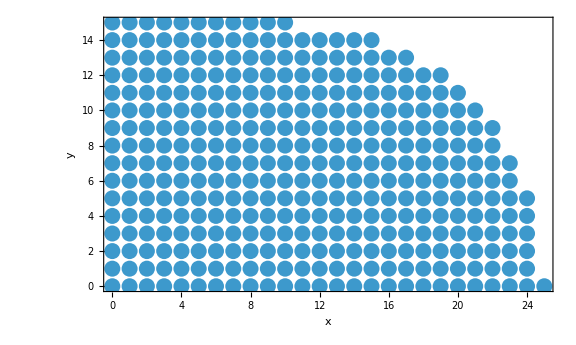

```mathematica
ListPlot[BunimovichData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.02]],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x", "y"},ImageSize->Large]
```

Obtain the index of {5,10} in  BunimovichData[“Coords”]:

```mathematica
BunimovichData["Mapping"][{5,10}]
```

91

Obtain the number of points in  BunimovichData[“Coords”]:

```mathematica
BunimovichData["Dimension"]
```

353

Obtain the parameters {semi-length l, semi-circle R} of the data BunimovichData[“Coords”]:

```mathematica
BunimovichData["Params"]
```

{10,15}

Obtain the type of geometry of BunimovichData (in case the name you use to store the data is not suggestive):

```mathematica
BunimovichData["Type"]
```

Bunimovich

## GenerateFullStadiumBasis[l,R]

generates the coordinate basis and mapping for the full (non-desymmetrized) Bunimovich stadium. It iterates over a bounding box defined by the semi-length L and radius R , selecting integer points that fall within either the central rectangular region or the semicircular ends.

For the full Bunimovich stadium with semi-length L and radius R, it returns an Association object with the following keys:

"Coords" : A flat list with all valid spatial coordinates {x, y} that form the basis of the position Hilbert subspace .

"Mapping" : An Association object that acts as a dictionary . It allows entering a coordinate (e . g ., {0, 0}) and obtaining its corresponding matrix index in O (1) time .

"Dimension" : An integer indicating the total dimension of the spatial basis .

"Params" : An Association containing the original input parameters, saved as <|"L" -> L, "R" -> R, "Symmetry" -> "None"|> .

"Type" : The label "BunimovichFull" to identify the generated geometry .

### Usage example

Coordinate basis and mapping for a full Bunimovich stadium of semi-length L=10 and radius R=15:

```mathematica
FullStadiumData=GenerateFullStadiumBasis[10,15];
```

The grid of FullStadiumData:

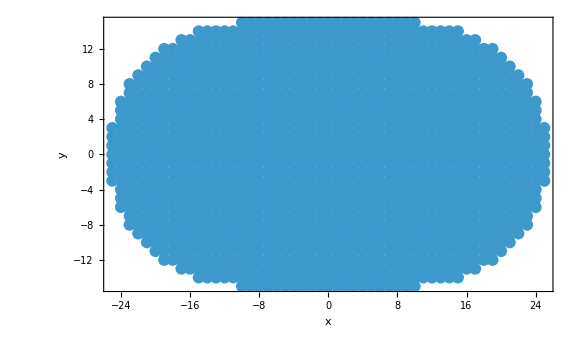

```mathematica
ListPlot[FullStadiumData["Coords"], 
 AspectRatio -> Automatic, 
 PlotStyle -> Directive[PointSize[0.015]], 
 Frame -> True, 
 FrameStyle -> Directive[Black, 20], 
 FrameLabel -> {"x", "y"}, 
 ImageSize -> Large]
```

Obtain the index of {0,15} (the top center point) in FullStadiumData:

```mathematica
FullStadiumData["Mapping"][{0,15}]
```

690

Obtain the total number of points in the full grid:

```mathematica
FullStadiumData["Dimension"]
```

1349

Obtain the parameters and symmetry metadata:

```mathematica
FullStadiumData["Params"]
```

<|L→10,R→15,Symmetry→None|>

Obtain the specific type of geometry:

```mathematica
FullStadiumData["Type"]
```

BunimovichFull

## GenerateRectangleBasis[Lx,Ly]

The function generates the coordinate basis and mapping for a rectangular billiard (integrable system). It selects integer points (x,y) that satisfy the rectangular geometry constraints 0 ≤ x ≤ Lx and 0 ≤ y ≤ Ly[cite: 206, 207, 208].

For the rectangular billiard with width Lx and height Ly, it returns an Association object with the following keys:

"Coords": A flat list with all valid spatial coordinates {x,y} that form the basis of the position Hilbert subspace.

"Mapping": An Association object that acts as a dictionary. It allows entering a coordinate (e.g., {0,0}) and obtaining its corresponding matrix index in O(1) time[cite: 208, 209].

"Dimension": An integer indicating the total dimension of the spatial basis.

"Params": An Association containing the original input parameters, saved as <|"Lx" → Lx, "Ly" → Ly|>.

"Type": The label "Rectangle" to easily identify the generated geometry.

### Usage example

Coordinate basis and mapping for a rectangular billiard of width Lx=10 and height Ly=5:

```mathematica
RectangleData=GenerateRectangleBasis[10,5];
```

The grid of RectangleData:

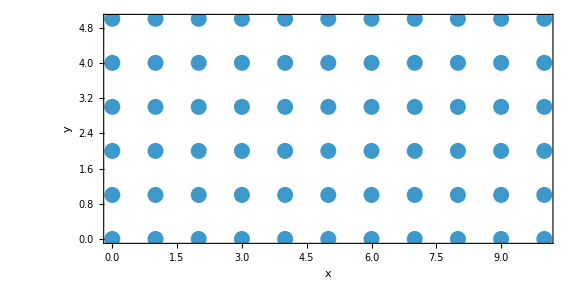

```mathematica
ListPlot[RectangleData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.02]],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x","y"},ImageSize->Large]
```

Obtain the index of {5, 2} in RectangleData["Coords"]:

```mathematica
RectangleData["Mapping"][{5,2}]
```

33

Obtain the number of points in RectangleData["Coords"]:

```mathematica
RectangleData["Dimension"]
```

66

Obtain the parameters {width Lx, height Ly} of the data RectangleData["Coords"]:

```mathematica
RectangleData["Params"]
```

<|Lx→10,Ly→5|>

Obtain the type of geometry of RectangleData (in case the name you use to store the data is not suggestive):

```mathematica
RectangleData["Type"]
```

Rectangle

## GenerateSinaiBasis[L,R]

The function generates the coordinate basis and the mapping association for the fundamental domain (1/8) of the Sinai billiard. This domain is defined within a square of semi-side L, excluding a disk of radius R, and restricted by diagonal symmetry (0 ≤ y ≤ x).

For the fundamental domain with semi-side L and radius R, it returns an Association object with the following keys:

"Coords": A flat list with all valid spatial coordinates {x, y} that form the basis of the 1/8 domain position subspace.

"Mapping": An Association object for O(1) coordinate-to-index lookups.

"Dimension": An integer indicating the total number of points in the desymmetrized grid.

"Params": An Association containing the geometric parameters: <|"L" → L, "R" → R, "Symmetry" → "1/8"|>.

"Type": The label "Sinai" identifying the geometry.

### Usage example

Coordinate basis for a Sinai fundamental domain with L=20 and R=10:

```mathematica
SinaiData=GenerateSinaiBasis[10,5]
```

<|Coords→{{4,3},{4,4},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{10,0},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}},Mapping→<|{4,3}→1,{4,4}→2,{5,0}→3,{5,1}→4,{5,2}→5,{5,3}→6,{5,4}→7,{5,5}→8,{6,0}→9,{6,1}→10,{6,2}→11,{6,3}→12,{6,4}→13,{6,5}→14,{6,6}→15,{7,0}→16,{7,1}→17,{7,2}→18,{7,3}→19,{7,4}→20,{7,5}→21,{7,6}→22,{7,7}→23,{8,0}→24,{8,1}→25,{8,2}→26,{8,3}→27,{8,4}→28,{8,5}→29,{8,6}→30,{8,7}→31,{8,8}→32,{9,0}→33,{9,1}→34,{9,2}→35,{9,3}→36,{9,4}→37,{9,5}→38,{9,6}→39,{9,7}→40,{9,8}→41,{9,9}→42,{10,0}→43,{10,1}→44,{10,2}→45,{10,3}→46,{10,4}→47,{10,5}→48,{10,6}→49,{10,7}→50,{10,8}→51,{10,9}→52,{10,10}→53|>,Dimension→53,Params→<|L→10,R→5,Symmetry→1/8|>,Type→Sinai|>

The grid of SinaiData (Fundamental Domain):

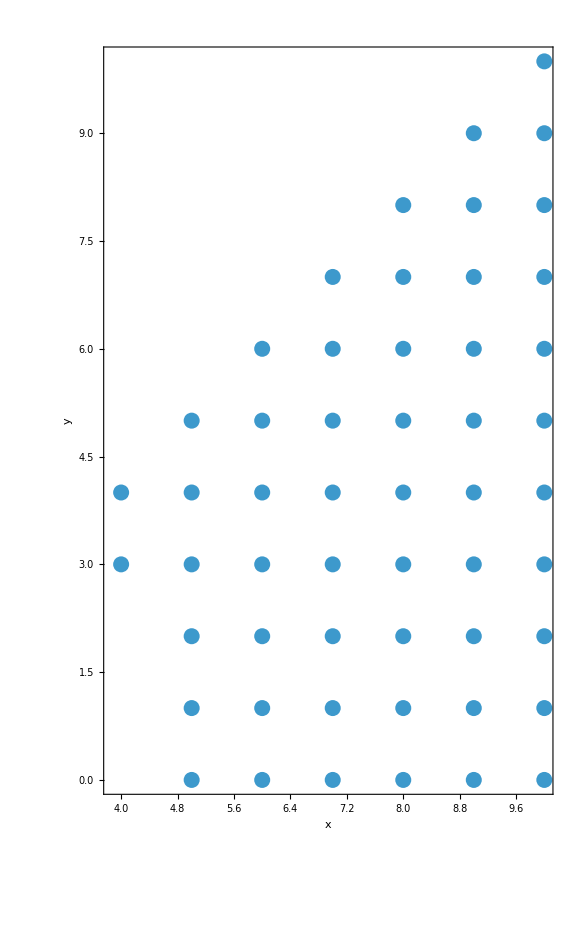

```mathematica
ListPlot[SinaiData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.02]],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x","y"},ImageSize->Large]
```

Obtain the index of {15, 5} in SinaiData:

```mathematica
SinaiData["Mapping"][{15,5}]
```

Missing[KeyAbsent,{15,5}]

## GenerateFullSinaiBasis[L,R]

generates the coordinate basis for the full Sinai billiard. The geometry consists of a square of side 2L (centered at the origin) with a circular obstacle of radius R removed from the center[cite: 47, 49, 54, 55].

For the full Sinai billiard, it returns an Association object with the following keys[cite: 49, 59]:

"Coords": A list of all coordinates {x, y} within the square [-L, L] such that x^2 + y^2 ≥ R^2[cite: 56, 57, 58].

"Mapping": An Association for fast coordinate mapping in the full Hilbert space[cite: 58, 59].

"Params": An Association containing: <|"L" → L, "R" → R, "Symmetry" → "None"|>[cite: 59].

### Usage example

Full Sinai billiard grid with L=15 and R=8:

```mathematica
FullSinaiData=GenerateFullSinaiBasis[15,8];
```

Visualize the full Sinai billiard grid:

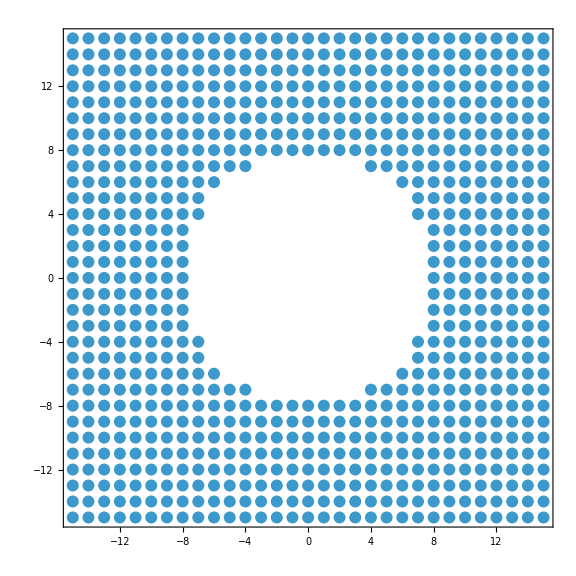

```mathematica
ListPlot[FullSinaiData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.015]],Frame->True,FrameStyle->Directive[Black,20],ImageSize->Large]
```

Total dimension of the full Sinai Hilbert space:

```mathematica
FullSinaiData["Dimension"]
```

768

## GenerateCardioidBasis[R]

The function generates the coordinate basis for a cardioid billiard defined by the algebraic equation (x^2 + y^2 + 2Rx)^2 ≤ 4R^2(x^2 + y^2). The cusp is located at the origin (0,0) and the main body extends towards negative x values.

For the cardioid billiard with scale parameter R, it returns an Association object with the following keys:

"Coords": A flat list with all valid spatial coordinates {x, y} that form the basis of the cardioid position subspace.

"Mapping": An Association object that acts as a dictionary for O(1) coordinate-to-index mapping.

"Dimension": An integer indicating the total number of points in the grid.

"Params": An Association containing the radius parameter: <|"R" → R|>.

"Type": The label "Cardioid" to identify the geometry.

### Usage example

Coordinate basis for a Cardioid billiard with R=10:

```mathematica
CardioidData=GenerateCardioidBasis[10];
```

The grid of CardioidData:

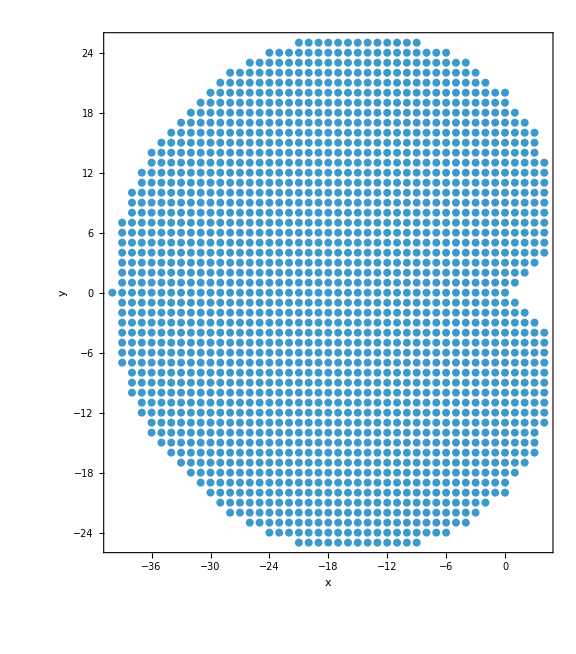

```mathematica
ListPlot[CardioidData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.01]],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x","y"},ImageSize->Large]
```

Obtain the index of the cusp at {0, 0}:

```mathematica
CardioidData["Mapping"][{0,0}]
```

1735

## GenerateEllipseBasis[A,B]

The function generates the coordinate basis for an elliptical billiard defined by (x/A)^2 + (y/B)^2 ≤ 1. If A = B, the function generates a circular billiard grid.

For the elliptical billiard with semi-axes A and B, it returns an Association object with the following keys:

"Coords": A flat list of coordinates {x, y} within the elliptical region.

"Mapping": An Association for fast coordinate lookups.

"Params": An Association containing: <|"A" → A, "B" → B|>.

"Type": Returns "Ellipse" or "Circle" if the axes are equal.

### Usage example

Elliptical grid with horizontal semi-axis A=30 and vertical semi-axis B=15:

```mathematica
EllipseData=GenerateEllipseBasis[30,15];
```

Visualize the elliptical grid:

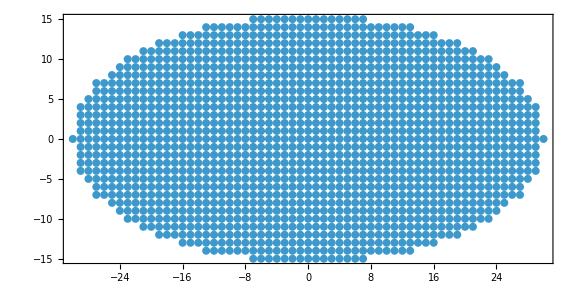

```mathematica
ListPlot[EllipseData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.01]],Frame->True,FrameStyle->Directive[Black,20],ImageSize->Large]
```

Check the geometry type:

```mathematica
EllipseData["Type"]
```

Ellipse

## BuildSymmetryIsometry[gridData,sector]

constructs the isometry matrix V for the specified symmetry sector of the given grid. This matrix projects the full Hilbert space into a specific symmetry subspace (e.g., parity sectors), which is essential for block-diagonalizing the Hamiltonian or evolution operators and reducing the computational cost of the simulation.

For the grid provided via gridData, the function calculates transformations based on the format of the sector argument:

String: Predefined labels such as "A1", "B2", "Even", "Odd", or group-specific labels like "C4v_A1".

List {sx, sy}: Numerical spatial parities (e.g., {1, -1} for x-even, y-odd) to define a sector in C2v symmetry.

Integer sy: A single parity value (1 or -1) to define a sector for bilateral symmetry along the y-axis.

Association chars: A dictionary mapping group operations to characters for C4v symmetry (8 isometries).

The function uses the grid definition from the Association and returns a SparseArray representing the isometry V. The resulting matrix has dimensions (4 * Dimension) × ReducedDimension.

### Usage example

Construct the isometry for the totally symmetric sector (A1) of a Bunimovich stadium:

```mathematica
grid=GenerateFullStadiumBasis[22,20];isometryA1=BuildSymmetryIsometry[grid,"A1"];
```

The grid in question:

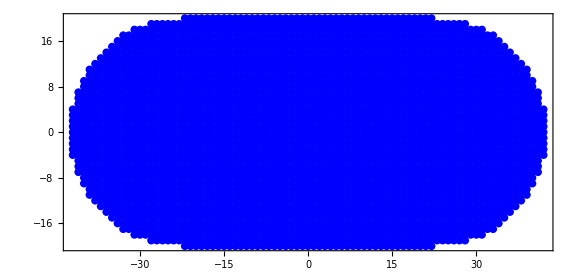

```mathematica
ListPlot[grid["Coords"], AspectRatio -> Automatic, 
  PlotStyle -> {PointSize[0.01], Blue}, Frame -> True, 
ImageSize->Large,LabelStyle->Directive[Black,FontSize->Scaled[.04]]]
```

Compare the dimensions of the full Hilbert space (4 internal states per node) vs. the reduced symmetric subspace:

```mathematica
{FullDim=4 grid["Dimension"],ReducedDim=Last[Dimensions[isometryA1]]}
```

{12388,3160}

Verify that the isometry is semi-unitary (V^†V = I):

```mathematica
Chop[ConjugateTranspose[isometryA1].isometryA1]==IdentityMatrix[ReducedDim]
```

True

## Neat examples

## 🎱 Quantum Walks in Billiards: A Beginner’s Guide

We will simulate a Discrete-Time Quantum Walk (DTQW) inside a 2D billiard geometry. If you are familiar with a particle in a box from quantum mechanics, imagine that particle moving on a discrete grid, carrying an internal “coin” (spin) that tells it which way to turn.

### 1. Define the geometry

First, you must decide one of these geometries:

Rectangle (integrable)

Ellipse (integrable)

Bunimovich (chaotic), you may choose to work in the dessymetrized or full stadium

Sinai (chaotic), you may choose to work in the dessymetrized or full billiard

Cardiod (chaotic), only full billiard available for now

Let us choose the Bunimovich dessymetrized billiard. First we must generate the basis for the position grid space:

```mathematica
?GenerateFullStadiumBasis
```

Total number of grid points (N): 2711

Total Hilbert Space Dimension (2N): 5422

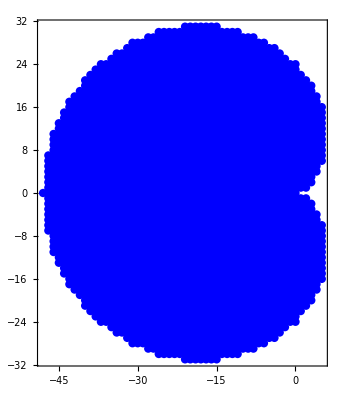

```mathematica
(*Define geometry parameters*)
xc=38; (*Length of the straight part*)
nu=xc;  (*Radius (width)*)

(*Generate the grid data*)
(*billiardData=GenerateStadiumBasis[xc,nu];*)
(*billiardData=GenerateFullStadiumBasis[xc,nu];*)
billiardData=GenerateCardioidBasis[12];
(*billiardData=GenerateSinaiBasis[120,75];
billiardData=GenerateRectangleBasis[60,40];*)

(*Let's see what we built*)
Print["Total number of grid points (N): ",billiardData["Dimension"]];
Print["Total Hilbert Space Dimension (2N): ",2*billiardData["Dimension"]];

(*Visualize the grid*)
ListPlot[billiardData["Coords"],PlotStyle->{PointSize[0.015],Blue},AspectRatio->Automatic,Frame->True]
```

### 2. Build the unitary operator

For a 2D walk, we need:

The Coin (C): Rotates the internal spin state.

The Shift operators (S_x, S_y): Move the particle Left/Right and Up/Down based on its spin.

The library function BuildShiftOperators does the heavy lifting of handling boundary conditions (bouncing off walls) using Sparse Arrays to save memory.

```mathematica
(*1. Construct Shift Operators*)
(*Returns a list {Wm,Wn}*)
{Sx,Sy}=BuildShiftOperators[billiardData];

(*2. Construct the Coin Operator*)
(*We use a standard Hadamard-like coin with angle Pi/4*)
dim=billiardData["Dimension"];
Coin1=Coin[Pi/4.,dim];
Coin2=Coin[Pi+0.1,dim];

(*{θ1,θ2}=RandomReal[{0,2Pi},2];
Coin1=Coin[θ1,dim];
Coin2=Coin[θ2,dim];*)

(*Check if the operators are Unitary (Preserve probability)*)
(*This is a good physics check!*)
unitaryCheck=UnitaryMatrixQ[Sy]&&UnitaryMatrixQ[Sx]&&UnitaryMatrixQ[Coin1]&&UnitaryMatrixQ[Coin2];
Print["Are our operators valid unitary matrices? ",unitaryCheck];
```

Are our operators valid unitary matrices? True

A single time step (U) in a 2D Split-Step Quantum Walk is often defined as: ψ_(t+1)=S_x C_2 S_y C_1

This means: Flip the coin, then Move vertrically, flip once again the coin, then Move Vertically.

```mathematica
(*Define the single step evolution operator*)
U=Sx.Coin2.Sy.Coin1
```

SparseArray[…]

```mathematica
U=Sy.Coin2.Sx.Coin1
```

SparseArray[…]

#### Level statistics, θ_1=θ_2=π/4

```mathematica
(*Exact diagonalization to obtain eigenvalues*)
eigenphases=Mod[Arg[Eigenvalues[Normal[U]]],2Pi];
```

```mathematica
{evals,evecs}=Transpose[SortBy[Transpose[Eigensystem[Normal[U]]],First]];
eigenphases=Sort@Mod[Arg[evals],2Pi];
```

```mathematica
Chop[evecs[[1]]]
Reverse[KroneckerProduct[IdentityMatrix[11],Pauli[1]].Chop[evecs[[1]]]]
```

{-0.0844425,0.216183+0.248079 ⅈ,0.383438,0.0963434-0.236913 ⅈ,-0.0225535-0.328283 ⅈ,-0.164102+0.187742 ⅈ,0.0319103-0.0319103 ⅈ,-0.201436-0.0200152 ⅈ,0.235648+0.0993976 ⅈ,-0.144881-0.0171574 ⅈ,-0.187742+0.164102 ⅈ,-0.0664867+0.146804 ⅈ,0.15659+0.128284 ⅈ,-0.152025-0.128721 ⅈ,0.0171574+0.144881 ⅈ,-0.0631991+0.152576 ⅈ,-0.056793+0.150819 ⅈ,-0.158452-0.132493 ⅈ,0.152025-0.128721 ⅈ,0.0162937+0.0393364 ⅈ,0.158452-0.132493 ⅈ,0.0164153+0.0396301 ⅈ}

{0.158452-0.132493 ⅈ,0.0164153+0.0396301 ⅈ,0.152025-0.128721 ⅈ,0.0162937+0.0393364 ⅈ,-0.056793+0.150819 ⅈ,-0.158452-0.132493 ⅈ,0.0171574+0.144881 ⅈ,-0.0631991+0.152576 ⅈ,0.15659+0.128284 ⅈ,-0.152025-0.128721 ⅈ,-0.187742+0.164102 ⅈ,-0.0664867+0.146804 ⅈ,0.235648+0.0993976 ⅈ,-0.144881-0.0171574 ⅈ,0.0319103-0.0319103 ⅈ,-0.201436-0.0200152 ⅈ,-0.0225535-0.328283 ⅈ,-0.164102+0.187742 ⅈ,0.383438+0. ⅈ,0.0963434-0.236913 ⅈ,-0.0844425+0. ⅈ,0.216183+0.248079 ⅈ}

```mathematica
billiardData["Mapping"][{-1,-1}*#]&/@billiardData["Coords"]
```

{11,10,9,8,7,6,5,4,3,2,1}

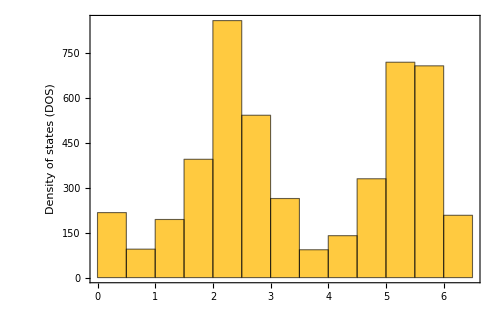

```mathematica
Histogram[eigenphases,Automatic,"Count",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

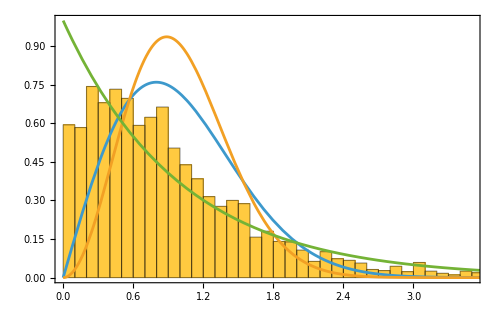

```mathematica
Show[
Histogram[Differences[Unfold[eigenphases]["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

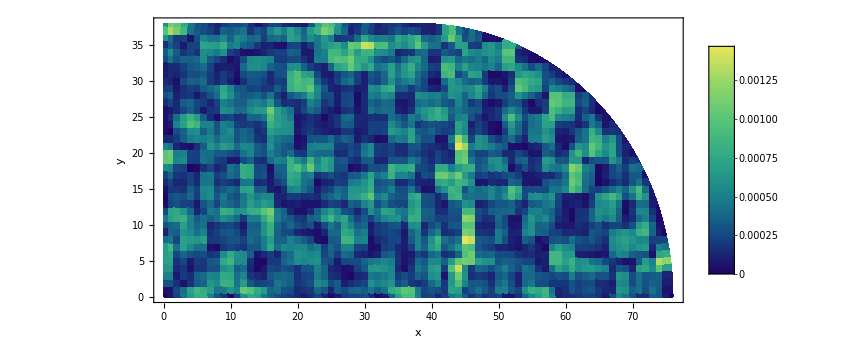

```mathematica
(*1. Extraemos parÃ¡metros.En Bunimovich.wl,"Params" es la lista {xc,nu}*){xcParameter,nuParameter}=billiardData["Params"];

(*2. Definimos la funciÃ.b3n lÃ.b3gica del Estadio (1/4 Desimetrizado)*)
StadiumRegionQ=Function[{x,y},Module[{inRectangle,inCircle},(*CondiciÃ.b3n 1:Parte rectangular (0<=x<=xc)*)inRectangle=(x<=xcParameter&&y<=nuParameter);
(*CondiciÃ.b3n 2:Parte circular (x>xc)*)(*Centrada en (xc,0) con radio nu*)inCircle=(x>xcParameter&&(x-xcParameter)^2+y^2<=nuParameter^2);
(*La regiÃ.b3n vÃ¡lida es la uniÃ.b3n de ambas,restringida al primer cuadrante*)(inRectangle||inCircle)&&(x>=0)&&(y>=0)]];

(*3. Generamos el Plot*)
ListDensityPlot[StateToPlotData[evecs[[4201]],billiardData["Coords"]],ColorFunction->"BlueGreenYellow",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0,(*Recorte exacto usando la geometrÃa del estadio*)RegionFunction->Function[{x,y,z},StadiumRegionQ[x,y]],Background->None,FrameLabel->{"x","y"}]
```

```mathematica
Manipulate[
ListDensityPlot[StateToPlotData[evecs[[i]],billiardData["Coords"]],ColorFunction->"SunsetColors",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0,(*Recorte exacto usando la geometrÃa del estadio*)RegionFunction->Function[{x,y,z},StadiumRegionQ[x,y]],Background->None,FrameLabel->{"x","y"}]
,{i,1600,1700}]
```

```mathematica
ipr=Table[Total[Total[Abs[evecs[[i,#;;#+1]]]^4]&/@Range[1,2*dim,2]],{i,2*dim}];
```

```mathematica
ListPlot[ipr,Filling->Axis,PlotRange->All]
```

### 3. Evolution simulation

```mathematica
(* 1. Inicializar la Geometría (Estadio de Bunimovich a 1/4) *)
R = 12;
l = 12;
GridData = GenerateBunimovichBasis[l, R];

Coords = GridData["Coords"];
TotalDim = GridData["Dimension"];

(* 2. Construcción de Operadores Unitarios (Espacio Completo de Hilbert) *)
S = BuildShiftOperators[GridData, CoinDimension -> 4];
CoinGlobal = 
KroneckerProduct[IdentityMatrix[TotalDim, SparseArray], SparseArray[GeneralizedGroverCoin[Pi/4.]]];

(* Operador de Paso Temporal *)
U = S . CoinGlobal;
```

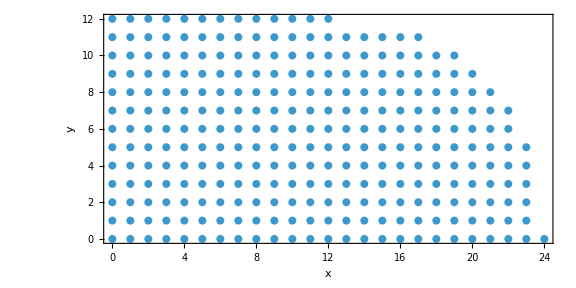

```mathematica
ListPlot[GridData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.01]],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x", "y"},ImageSize->Large]
```

```mathematica
(* 3. Estado Inicial (Paquete Gaussiano centrado espacialmente) *)
SigmaGauss = 0.1;
CentroGrid = Round[Mean[Coords]];

(* Base espacial Gaussiana normalizada *)
AmplitudesEspaciales = Chop@Normalize[
    Exp[-((#[[1]] - CentroGrid[[1]])^2 + (#[[2]] - CentroGrid[[2]])^2) / (2 * SigmaGauss^2)] & /@ Coords
];

(* Moneda inicial simétrica (Arriba, Abajo, Derecha, Izquierda) *)
EstadoMoneda = {1, 1, 1, 1} / 2.;

(* Producto tensorial O(N): |Psi_0> = |Psi_espacial> (x) |Psi_moneda> *)
PsiInicial = Flatten[Outer[Times, AmplitudesEspaciales, EstadoMoneda]];
```

```mathematica
(* 4. Evolución Temporal Eficiente (30 pasos) *)
tMax =30;
EstadosEvolucion = NestList[U . # &, PsiInicial, tMax];
```

```mathematica
(* 5. Cálculo de Distribución de Probabilidad Espacial *)
ExtraerProbabilidadEspacial[PsiVector_] := Total /@ Partition[Abs[PsiVector]^2, 4];
ProbabilidadesPorPaso = ExtraerProbabilidadEspacial /@ EstadosEvolucion;
```

```mathematica
(* 6. Generación de Animación Visual *)
(* Fijamos la escala de color usando la probabilidad máxima global para evitar parpadeos visuales *)
ProbabilidadMaxima = Max[ProbabilidadesPorPaso];

CrearGrafico[IndicePaso_] := Module[
    {DatosPlot},
    (* Enlazar coordenadas con su probabilidad *)
    DatosPlot = MapThread[Append[#1, #2] &, {Coords, ProbabilidadesPorPaso[[IndicePaso]]}];
    
    (* --- Preparación de variables logarítmicas --- *)
ProbMin = 2*10.^-5; (* Umbral para evitar Log[0]. Puedes cambiarlo a 10^-5 o 10^-6 si quieres ver más ruido *)
LogPMin = Log10[ProbMin];
LogPMax = Log10[ProbabilidadMaxima];

ListDensityPlot[DatosPlot,
    ColorFunctionScaling -> False,
    ColorFunction -> Function[prob, 
        If[prob <= ProbMin, 
            White, 
            ColorData["DarkRainbow"][Clip[(Log10[prob] - LogPMin) / (LogPMax - LogPMin), {0, 1}]]
        ]
    ],
    PlotRange -> {{0, l + R + 1}, {0, R + 1}, {0, ProbabilidadMaxima}},
    Mesh -> False,
    InterpolationOrder -> 0, 
    FrameLabel -> {"X", "Y"},
    PlotLabel -> Style["t = " <> ToString[IndicePaso - 1], 16, Bold],
    ImageSize -> Large,
    Background -> White,
    AspectRatio -> Automatic,
    LabelStyle -> Directive[Black, 20], 
    
    (* --- Barra de leyenda en escala logarítmica --- *)
    PlotLegends -> Placed[
        BarLegend[{
            Function[logProb, 
                ColorData["DarkRainbow"][Clip[(logProb - LogPMin) / (LogPMax - LogPMin), {0, 1}]]
            ], 
            {LogPMin, LogPMax}
        }, 
        (* Generamos automáticamente las etiquetas como 10^-4, 10^-3... *)
        Ticks -> ({#, Superscript[10, #]} & /@ Range[Round[LogPMin], Ceiling[LogPMax]]),
        LegendLabel -> Style["Probabilidad", 14], 
        LegendMarkerSize -> 300], 
        Right
    ],
    
    (* --- 1. Evitar que el color se desparrame fuera del billar --- *)
    RegionFunction -> Function[{x, y, prob},
        x >= 0 && y >= 0 && 
        y <= If[x <= l, 
                  R, 
                  Sqrt[Max[0, R^2 - (x - l)^2]]]
    ],
    
    (* --- 2. Dibujar la frontera del billar de Bunimovich (1/4) --- *)
    Epilog -> {
        Directive[Thick, Black],
        (* Pared inferior (Eje X) *)
        Line[{{0, 0}, {l + R, 0}}],
        (* Pared izquierda (Eje Y) *)
        Line[{{0, 0}, {0, R}}],
        (* Techo recto superior *)
        Line[{{0, R}, {l, R}}],
        (* Tapa semicircular derecha *)
        Circle[{l, 0}, R, {0, Pi/2}]
    }
]
];
```

```mathematica
(* Mostrar el resultado como un reproductor de video interactivo *)
AnimacionDTQW = ListAnimate[CrearGrafico /@ Range[Length[EstadosEvolucion]],1]
```